## 1x2 φ =0.3

{a→0.0305262,b→-0.37504}

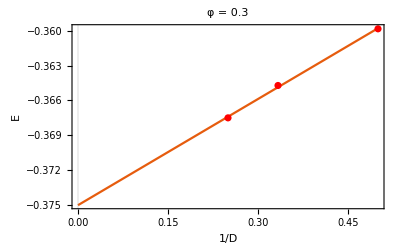

```mathematica
energy ={-0.35982695274452925,-0.36471546435869906,-0.3675082986177153};
data=Table[{1/d,energy[[d-1]]},{d,2,4}];
fit=FindFit[data,a x +b,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,1/2},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["E"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{"φ = 0.3"}]],LabelStyle->{GrayLevel[0]}]
```

{a→0.399681,b→0.139861}

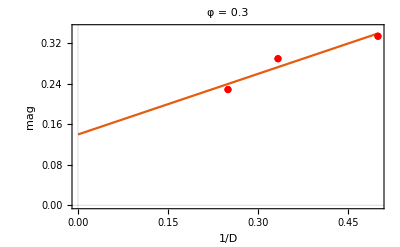

```mathematica
mag={0.3341664105042756,0.28969304876019186,0.22871118677927021};
data=Table[{1/d,mag[[d-1]]},{d,2,4}];
fit =FindFit[data,a x+b ,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,0.5},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["mag"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{"φ = 0.3"}]],LabelStyle->{GrayLevel[0]},PlotRange->{{0,0.5},{0,0.35}}]
```

{a→-0.00562723,b→0.0677778}

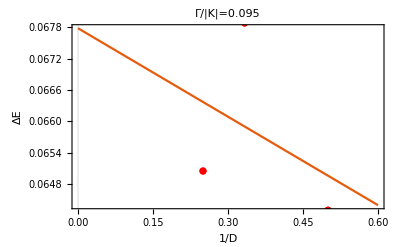

```mathematica
ΔE={0.06430541878314935,0.06787855505565239,0.06505340978457512};
data=Table[{1/d,ΔE[[d-1]]},{d,2,4}];
fit =FindFit[data,a x+b ,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,0.6},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["ΔE"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"Γ","/"}],"|","K","|"}],"=","0.095"}]],LabelStyle->{GrayLevel[0]}]
```

## 1x2 Γ=0.03

{a→0.0149567,b→-0.201592}

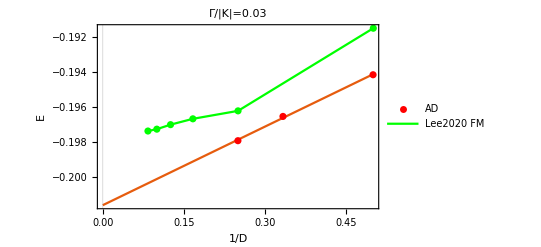

```mathematica
Lee2020={{0.0835555556,-0.1973560606},
{0.1000000000,-0.1972500000},
{0.1253333333,-0.1969924242},
{0.1666666667,-0.1966590909},
{0.2502222222,-0.1962045455},
{0.5004444444,-0.1914848485}};
energy ={-0.19414182077659287,-0.1965226483068633,-0.1979089951956053,-0.19795203827624958};
data=Table[{1/d,energy[[d-1]]},{d,2,4}];
fit=FindFit[data,a x +b,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,1/2},PlotTheme->"Scientific"],ListPlot[{data,Lee2020},PlotStyle->{Red,Green},PlotLegends->{"AD","Lee2020 FM"},Joined->{False,True},Mesh->All],FrameLabel->{{HoldForm["E"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"Γ","/"}],"|","K","|"}],"=","0.03"}]],LabelStyle->{GrayLevel[0]},PlotRange->All]
```

{a→0.402882,b→0.}

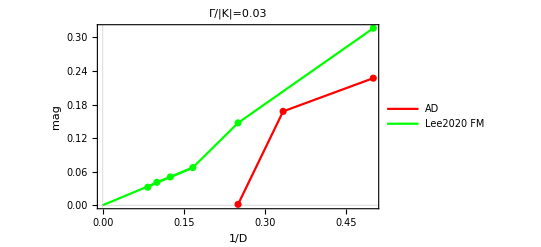

```mathematica
Lee2020={{0.0832000000,0.0321019108},
{0.1000000000,0.0408917197},
{0.1248000000,0.0504458599},
{0.1664000000,0.0672611465},
{0.2500000000,0.1471337580},
{0.5000000000,0.3164331210}};
mag={0.22714551994594442,0.16773842057901422,0.001443417004068677};
data=Table[{1/d,mag[[d-1]]},{d,2,4}];
fit =FindFit[Lee2020[[1;;4]],a x ,{a,b},x]
Show[Plot[a x/.fit,{x,0,0.166},PlotStyle->Green,PlotTheme->"Scientific"],ListPlot[{data,Lee2020},PlotStyle->{Red,Green},PlotLegends->{"AD","Lee2020 FM"},Joined->{True,True},Mesh->All],FrameLabel->{{HoldForm["mag"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"Γ","/"}],"|","K","|"}],"=","0.03"}]],LabelStyle->{GrayLevel[0]},PlotRange->All]
```

{a→0.0391571,b→-0.00456989}

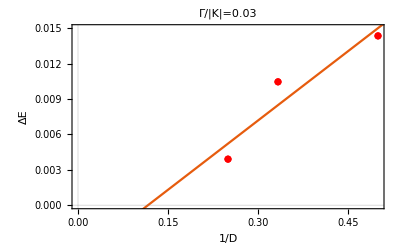

```mathematica
ΔE={0.014350786069645382,0.010456058963646687,0.0039036517525364843};
data=Table[{1/d,ΔE[[d-1]]},{d,2,4}];
fit =FindFit[data,a x+b ,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,0.6},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["ΔE"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"Γ","/"}],"|","K","|"}],"=","0.03"}]],LabelStyle->{GrayLevel[0]},PlotRange->{{0,0.5},{0,0.015}}]
```

## 1x2 Γ=0.095

{a→0.0130868,b→-0.213326}

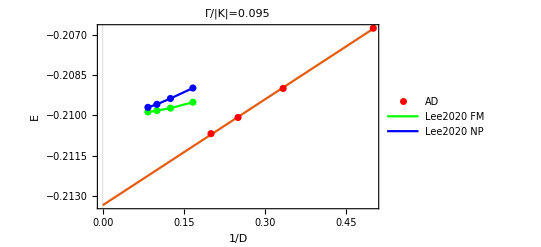

```mathematica
Lee2020={{{0.0833684211,-0.2098699029},
{0.1000000000,-0.2098210818},
{0.1250526316,-0.2097278779},
{0.1666315789,-0.2095092926}},{{0.0834736842,-0.2096990291},
{0.1000000000,-0.2095869626},
{0.1250526316,-0.2093705964},
{0.1665263158,-0.2089822469}}};
energy ={-0.20676516915208426,-0.2089967519835565,-0.2100743212175767,-0.21067447574497888};
data=Table[{1/d,energy[[d-1]]},{d,2,5}];
fit=FindFit[data,a x +b,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,1/2},PlotTheme->"Scientific"],ListPlot[{data,Lee2020[[1]],Lee2020[[2]]},PlotStyle->{Red,Green,Blue},PlotLegends->{"AD","Lee2020 FM","Lee2020 NP"},Joined->{False,True,True},Mesh->All],FrameLabel->{{HoldForm["E"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"Γ","/"}],"|","K","|"}],"=","0.095"}]],LabelStyle->{GrayLevel[0]},PlotRange->All]
```

{a→0.620766,b→0.}

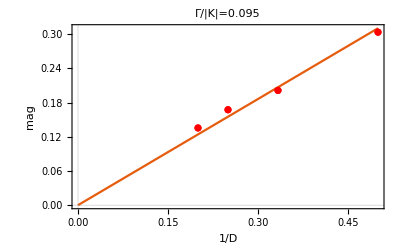

```mathematica
mag={0.3034907216895013,0.20131151562348848,0.1674002073374355,0.1354730690169634};
data=Table[{1/d,mag[[d-1]]},{d,2,5}];
fit =FindFit[data,a x ,{a,b},x]
Show[Plot[a x/.fit,{x,0,0.5},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["mag"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"Γ","/"}],"|","K","|"}],"=","0.095"}]],LabelStyle->{GrayLevel[0]}]
```

{a→0.0294509,b→0.0172171}

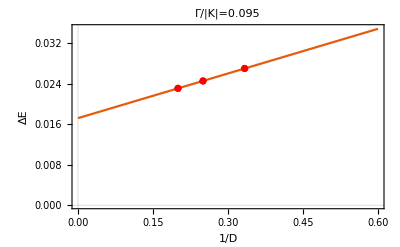

```mathematica
ΔE={0.017843771321760567,0.027036709796111273,0.024572783879574754,0.02311168906030161};
data=Table[{1/d,ΔE[[d-1]]},{d,3,5}];
fit =FindFit[data,a x+b ,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,0.6},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["ΔE"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"Γ","/"}],"|","K","|"}],"=","0.095"}]],LabelStyle->{GrayLevel[0]},PlotRange->{{0,0.6},{0,0.035}}]
```

## 1x2 Γ=0.2

{a→-0.0500969,b→0.0517041,c→-0.247127}

{a→0.,b→0.0160495,c→-0.241495}

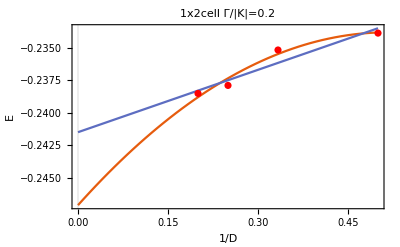

```mathematica
energy ={-0.2338456066900379,-0.23514879447046375,-0.23788413119246593,-0.2385032141944618};
data=Table[{1/d,energy[[d-1]]},{d,2,5}];
fit1=FindFit[data,a*x^2+b x+c,{a,b,c},x]
fit2=FindFit[data,b x+c,{a,b,c},x]
Show[Plot[{a*x^2+b x+c/.fit1,b x+c/.fit2},{x,0,1/2},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["E"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"1x2cell Γ","/"}],"|","K","|"}],"=","0.2"}]],LabelStyle->{GrayLevel[0]}]
```

{a→0.,b→0.969881,c→-0.166831}

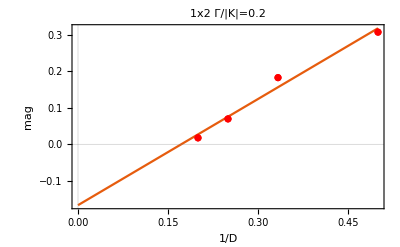

```mathematica
mag={0.30746275238729925,0.18268586849101562,0.06958782627704607,0.017618806302343405};
data=Table[{1/d,mag[[d-1]]},{d,2,5}];
fit =FindFit[data,b x+c ,{a,b,c},x]
Show[Plot[b x+c/.fit,{x,0,0.5},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["mag"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"1x2 Γ","/"}],"|","K","|"}],"=","0.2"}]],LabelStyle->{GrayLevel[0]}]
```

{a→-0.126153,b→0.0795865}

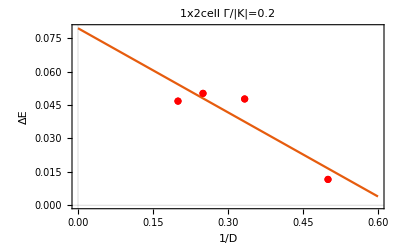

```mathematica
ΔE={0.011589059627032784,0.04776973477532587,0.05028348503366667,0.046807601852071064};
data=Table[{1/d,ΔE[[d-1]]},{d,2,5}];
fit =FindFit[data,a x+b ,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,0.6},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["ΔE"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"1x2cell Γ","/"}],"|","K","|"}],"=","0.2"}]],LabelStyle->{GrayLevel[0]}]
```

## 1x3 Γ=0.2

{a→0.0244885,b→-0.000089438,c→-0.239804}

{a→0.,b→0.0173393,c→-0.242557}

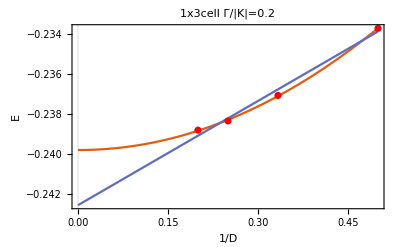

```mathematica
energy ={-0.23373090256813112,-0.23707997639253897,-0.2383529284912592,-0.2388118539470231};
data=Table[{1/d,energy[[d-1]]},{d,2,5}];
fit1=FindFit[data,a*x^2+b x+c,{a,b,c},x]
fit2=FindFit[data,b x+c,{a,b,c},x]
Show[Plot[{a*x^2+b x+c/.fit1,b x+c/.fit2},{x,0,1/2},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["E"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"1x3cell Γ","/"}],"|","K","|"}],"=","0.2"}]],LabelStyle->{GrayLevel[0]}]
```

{a→0.,b→0.544214,c→0.0512101}

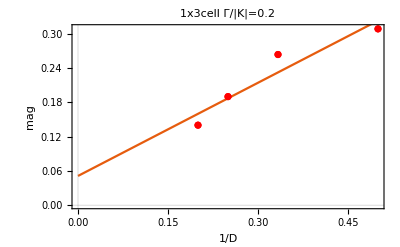

```mathematica
mag={0.3088910834244099,0.26396769234424855,0.19021188148973192,0.14017766456570147};
data=Table[{1/d,mag[[d-1]]},{d,2,5}];
fit =FindFit[data,b x+c ,{a,b,c},x]
Show[Plot[b x+c/.fit,{x,0,0.5},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["mag"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"1x3cell Γ","/"}],"|","K","|"}],"=","0.2"}]],LabelStyle->{GrayLevel[0]},PlotRange->{{0,0.5},{0,0.31}}]
```

{a→-0.0942406,b→0.0649243}

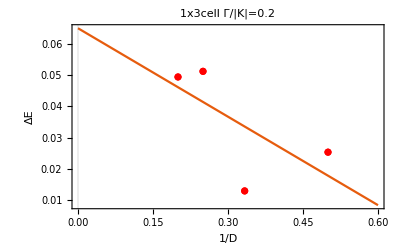

```mathematica
ΔE={0.025318678200659722,0.01293260747551876,0.05115122481202371,0.049352601749088516};
data=Table[{1/d,ΔE[[d-1]]},{d,2,5}];
fit =FindFit[data,a x+b ,{a,b},x]
Show[Plot[a x+b/.fit,{x,0,0.6},PlotTheme->"Scientific"],ListPlot[data,PlotStyle->Red],ListPlot[data,PlotStyle->Red],FrameLabel->{{HoldForm["ΔE"],None},{HoldForm["1/D"],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{RowBox[{"1x3cell Γ","/"}],"|","K","|"}],"=","0.2"}]],LabelStyle->{GrayLevel[0]}]
```

## 1x2 Kitaev

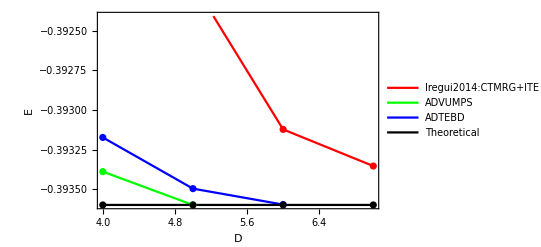

```mathematica
CTMRG={{0.14275668073136427,-0.3933542168674699},
{0.16666666666666669,-0.3931228915662651},
{0.200070323488045,-0.3921975903614458},
{0.250351617440225,-0.3915228915662651}};
ADVUMPS ={-0.37878655734769523,-0.38473944160091056,-0.1966947649843151*2,-0.3936};
ADTEBD={-0.37959959,-0.39317356,-0.39349701,-0.39359769};
Show[ListPlot[{Table[{8-i,CTMRG[[i,2]]},{i,1,4}],Table[{i+1,ADVUMPS [[i]]},{i,3,4}],Table[{i+2,ADTEBD[[i]]},{i,2,4}],Table[{i,-0.3936},{i,4,7}]},PlotTheme->"Scientific",PlotStyle->{Red,Green,Blue,Black},PlotLegends->{"Iregui2014:CTMRG+ITE","ADVUMPS","ADTEBD","Theoretical"},Joined->{True,True,True,True},Mesh->All],FrameLabel->{{HoldForm["E"],None},{HoldForm["D"],None}},LabelStyle->{GrayLevel[0]},PlotRange->All]
```

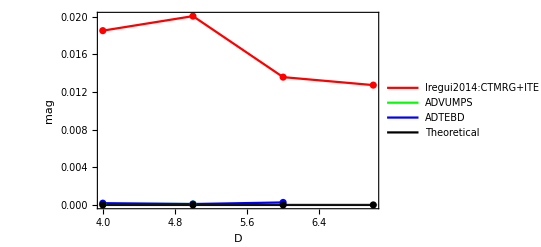

```mathematica
CTMRG={0.012741312741312752,0.01359073359073358,0.02007722007722007,0.018532818532818532};
ADVUMPS ={0.0001,0.0001,0.0001,0.0001};
ADTEBD={0.272110129,.0001872923,0.0000972301,0.00026596848};
Show[ListPlot[{Table[{8-i,CTMRG[[i]]},{i,1,4}],Table[{i+1,ADVUMPS [[i]]},{i,3,4}],Table[{i+2,ADTEBD[[i]]},{i,2,4}],Table[{i,0},{i,4,7}]},PlotTheme->"Scientific",PlotStyle->{Red,Green,Blue,Black},PlotLegends->{"Iregui2014:CTMRG+ITE","ADVUMPS","ADTEBD","Theoretical"},Joined->{True,True,True,True},Mesh->All],FrameLabel->{{HoldForm["mag"],None},{HoldForm["D"],None}},LabelStyle->{GrayLevel[0]},PlotRange->All]
```